# Sample complexity plots

This notebook plots the sample complexity and variation of sample complexity with network size.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

02/08/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the ranges of values to be used for each parameter.

```mathematica
channelType={{"AWGN"},{"Nakagami",0.5},{"Nakagami",2},{"Rayleigh"},{"Rice",5}};
nRange={1,2,3,4,5,10,20,50,100};
snrdb=-21;
γ=10^(snrdb/10);
pf=10/100;
pd=90/100;
```

## Calculations

Generate sample complexity data:

```mathematica
data=Table[{n,SampleComplexity[γ,pf,pd,n,ChannelType->c,DatabaseLookup->True]},{c,channelType},{n,nRange}];
```

```mathematica
normalisedData=Table[{n,SampleComplexity[γ,pf,pd,n,ChannelType->c,DatabaseLookup->True]/SampleComplexity[γ,pf,pd,n,ChannelType->"AWGN",DatabaseLookup->True]},{c,channelType},{n,nRange}];
```

## Results

### Variation of sample complexity with network size

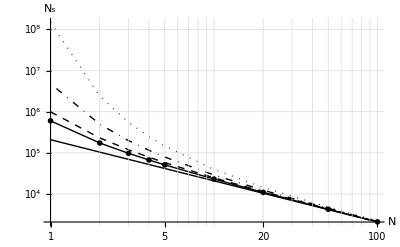

```mathematica
ListLogLogPlot[data,plotOptions,PlotLegend->Table[LegendFormat[c],{c,channelType}],legendOptions]
```

### Variation of normalised sample complexity with network size

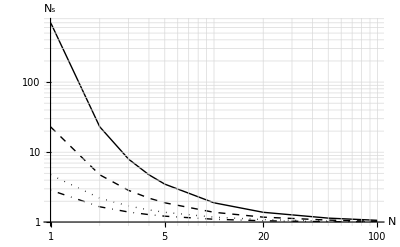

```mathematica
ListLogLogPlot[normalisedData[[2;;All]],plotOptions,PlotLegend->Table[LegendFormat[c],{c,channelType[[2;;All]]}],legendOptions]
```